```mathematica
(*save the directory of the notebook in variable*)
Clear[dir];
dir = NotebookDirectory[];
```

```mathematica
(*set total frames, frame interval for image import*)
totalFrames=8100;
frameInterval=5;
timeInterval = 0.115;
frames = Table[i,{i,1,totalFrames,frameInterval}];
```

```mathematica
(*Import images from tif file. Gives a list of images: e.g. 400 frame 512x512 tif file generates a list of 400 512x512 matrices*)
images=Import["/Volumes/Morne/Data Göteborg/2022-09/26092022/device 1/2.8mM w 50uM ATP cont 3.tif",{"Data",frames}];
```

Import::nffil: File D:\Data Göteborg\Mathematica scripts\STC\26092022 1st device.lif - 2,8mM Glc 50uM ATP 3.tif not found during Import.

```mathematica
(*converts image data so we instead have a list of each pixels values over time*)
pixelData=Transpose[images,{3,2,1}];
Dimensions[pixelData]
```

```mathematica
(*Export pixel data for qick import if needed elsewhere*)
Export[StringJoin[dir,"pixelData.mx"],pixelData];
```

```mathematica
pixelData=Import[StringJoin[dir,"pixelData.mx"]];
Dimensions[pixelData]
```

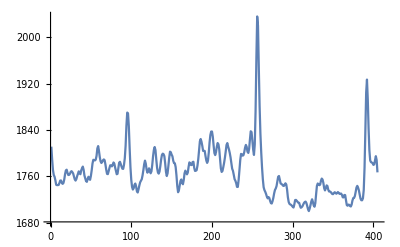

```mathematica
(*Plots the time course for a single pixel. Select a pixel by choosing its x and y position*)
ListLinePlot[GaussianFilter[pixelData[[350,350]],3],PlotRange->All, Axes-.False,Frame->True, ImageSize->400,FrameLabel->{"frames","Intensity (AU)"}]
```

```mathematica
(*Gets the max value for each pixel through the time course*)
Monitor[maxValues=Table[Max[pixelData[[i,j]]],{i,1,Length[pixelData]},{j,1,Length[pixelData]}];{i,j},{100*N[i/Length[pixelData]],100*N[j/Length[pixelData]]}];
```

```mathematica
(*Gets the 10th highest value for each pixel through the time course*)
Monitor[highPercentileValues=Table[TakeLargest[pixelData[[i,j]],10][[-1]],{i,1,Length[pixelData]},{j,1,Length[pixelData]}];{i,j},{100*N[i/Length[pixelData]],100*N[j/Length[pixelData]]}];
```

```mathematica
(*get the mean between maxImage and the highPercentile image to be used as the sample image*)
GraphicsRow[{
ImageAdjust[Image[maxValues]],
ImageAdjust[Image[highPercentileValues]],
ImageAdjust[Image [sampleImage=Mean[{maxValues,highPercentileValues}]]]
}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Determine kernel size for filtering*)
kernelR=2;
kernelSmall=GaussianFilter[sampleImage,kernelR];
kernelLarge=GaussianFilter[sampleImage,2*kernelR];
```

```mathematica
(*Generate bandpass image*)
ImageAdjust[Image[bandPassImage=(kernelSmall-kernelLarge)]]
```

-Graphics-

```mathematica
(*Distance transform. Value can be adjusted to distinguish between background and foreground*)
distanceTranceform=DistanceTransform[Image[bandPassImage],40]
```

-Graphics-

```mathematica
(*Setup for watershed segmentation*)
seeds=MaxDetect[distanceTranceform]
background = MorphologicalBinarize[distanceTranceform]
```

-Graphics-

-Graphics-

```mathematica
(*Segmentation by watershed. Can be adjusted by changing the Method: MinimumSaliency value*)
watershedComponents=WatershedComponents[seeds,background,Method->{"MinimumSaliency", 0.8}];
Colorize[watershedComponents]
```

-Graphics-

```mathematica
(*Generate list of masks, labels and centroids of components which have less than 1000 pixels and more than 4 pixels*)
maskList=ComponentMeasurements[watershedComponents,"Mask",1000>#Count>4&];
maskLabels=ComponentMeasurements[watershedComponents,"Label",1000>#Count>4&];
maskCentroids=ComponentMeasurements[watershedComponents,"Centroid",1000>#Count>4&];
```

```mathematica
(*Matrix containing the x and y position of each pixel*)
ijMat=Table[{i,j},{i,1,512},{j,1,512}];
```

```mathematica
(*Get the pixel positions for each mask*)
Monitor[maskPixels=Table[DeleteCases[Flatten[DeleteCases[ijMat*Normal[maskList[[n,2]]],0,Infinity],1],{},Infinity],{n,1,Length[maskList]}];n,100*N[n/Length[maskList]]];
```

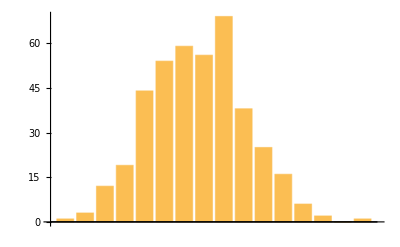

1611.32

40.1412

23.9545

573.817

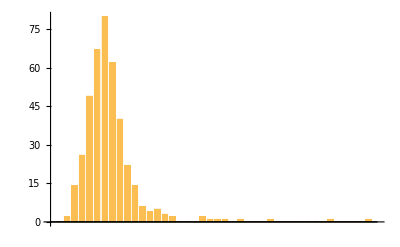

1753.42

47.8668

2291.23

```mathematica
(*To demostrate the difference between a pixel which has a signal and one which does not. A pixel with no signal will have a normal distribution of values. A pixel with a signal will have a long tail to its right and a high variance*)

BarChart[BinCounts[pixelData[[1,1]],10],PlotLabel->"Pixel with no signal"]
Grid[{
{"Mean: "<>ToString[N[Mean[pixelData[[1,1]]]]],
"Stdev: "<>ToString[N[StandardDeviation[pixelData[[1,1]]]]],
"Variance: "<>ToString[N[Variance[pixelData[[1,1]]]]]
}
}]

BarChart[BinCounts[pixelData[[351,355]],10],PlotLabel->"Pixel with signal"]
Grid[{
{"Mean: "<>ToString[N[Mean[pixelData[[351,351]]]]],
"Stdev: "<>ToString[N[StandardDeviation[pixelData[[351,351]]]]],
"Variance: "<>ToString[N[Variance[pixelData[[351,351]]]]]}
}]
```

```mathematica
ZScore[x_,σ_,μ_]:=(x-μ)/σ
```

```mathematica
(*Get the mean data for each mask*)
meanSignalData=Table[Mean[Table[pixelData[[maskPixels[[n]][[i,1]],maskPixels[[n]][[i,2]]]],{i,1,Length[maskPixels[[n]]]}]],{n,1,Length[maskPixels]}];
```

```mathematica
(*Get the sum data for each mask*)
sumSignalData=Table[Total[Table[pixelData[[maskPixels[[n]][[i,1]],maskPixels[[n]][[i,2]]]],{i,1,Length[maskPixels[[n]]]}]],{n,1,Length[maskPixels]}];
```

```mathematica
(*Export data*)
(*Export[StringJoin[dir,"meanSignal.mx"],meanSignalData]
Export[StringJoin[dir,"sumSignal.mx"],sumSignalData]*)
```

C:\My Documents\Image analysis files\26092022\meanSignal.mx

C:\My Documents\Image analysis files\26092022\sumSignal.mx

```mathematica
(*Export the component centroids and labels numbers*)
(*Export[StringJoin[dir,"componentCentroids.mx"],maskCentroids]
Export[StringJoin[dir,"componentNumbers.mx"],maskLabels]*)
```

C:\My Documents\Image analysis files\26092022\componentCentroids.mx

C:\My Documents\Image analysis files\26092022\componentNumbers.mx